### North America

```mathematica
america =Mod[# +1,2]&/@ Import["/home/sonja/Documents/Cluster-calculation/Mathematica/sa.nc", {"Datasets", "topo"}];
```

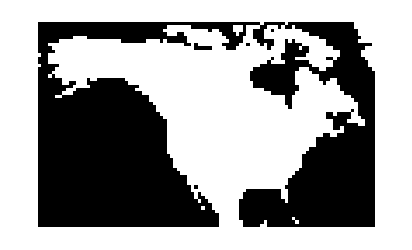

```mathematica
ArrayPlot[america,DataReversed->True]
```

```mathematica
Export["/home/sonja/Documents/Cluster-calculation/mask/North-America-mask.txt",america,"Table"];
```

```mathematica
america =Mod[# +2,2]&/@ Import["/home/sonja/Documents/Composites/Mathematica/sm.nc", {"Datasets", "topo"}];
```

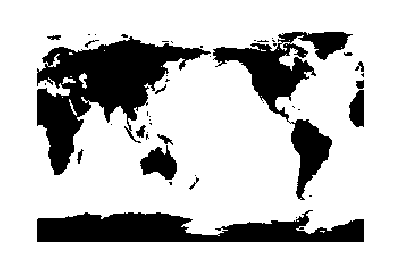

```mathematica
ArrayPlot[america,DataReversed->True]
```

```mathematica
Export["/home/sonja/Documents/Composites/mask/sst-mask.txt",america,"Table"];
```

### Europe + Turkey

```mathematica
eu=Graphics[{Black,CountryData["Europe","Polygon"],CountryData["Turkey","Polygon"]},Frame->False,PlotRange->{{-12,45},{25.5,72}},ImageSize->{77,63}]
```

-Graphics-

```mathematica
ArrayPlot[Reverse[ImageData[eu][[;;,;;,1]]],DataReversed->True]
```

```mathematica
Export["/home/sonja/Documents/Cluster-calculation/mask/Europe-mask.txt",Reverse[ImageData[eu]⟦;;,;;,1⟧],"Table"];
```